```mathematica
(* Testing SystemSolver *)
Δc1=0.01;
Δc2=0.02;
popsize=10^4;
nexttimestep=1000;
```

{{n1'[t]==1.03 (1-n1[t]/10000) n1[t],n1[0]==10000},{{n1[t]→10000}}}

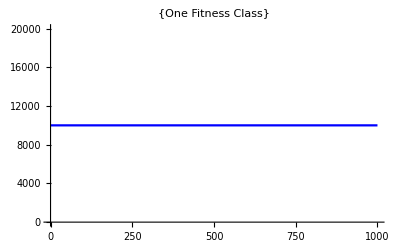

{{n1'[t]==1.03 (1-n1[t]/10000) n1[t],n1[0]==9500},{{n1[t]→10000/(1+ⅇ^(-1.03 t)/19)}}}

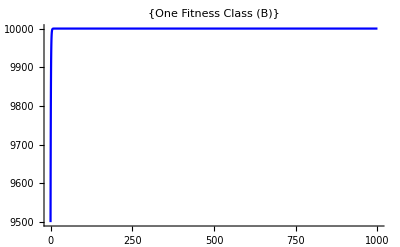

{{n1'[t]==1.03 (1-n1[t]/10000) n1[t],n1[0]==10500},{{n1[t]→10000/(1-ⅇ^(-1.03 t)/21)}}}

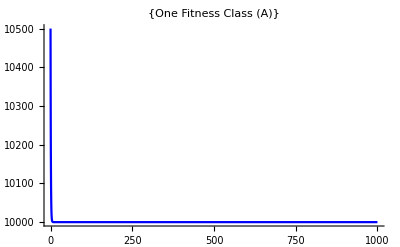

{{n1'[t]==n1[t] (1.03+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n2'[t]==n2[t] (1.05+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n3'[t]==(1.04+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000) n3[t],n1[0]==9890,n2[0]==100,n3[0]==10},{{n1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n3[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}}

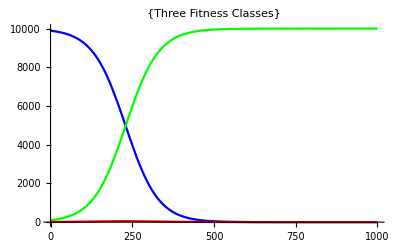

{{n1'[t]==n1[t] (1.03+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n2'[t]==n2[t] (1.05+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n3'[t]==(1.04+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000) n3[t],n1[0]==9500,n2[0]==100,n3[0]==10},{{n1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n3[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}}

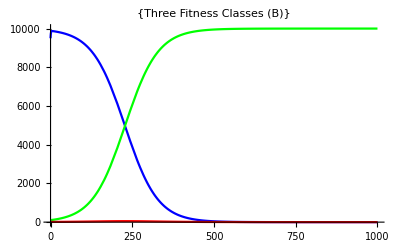

{{n1'[t]==n1[t] (1.03+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n2'[t]==n2[t] (1.05+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000),n3'[t]==(1.04+(-1.03 n1[t]-1.05 n2[t]-1.04 n3[t])/10000) n3[t],n1[0]==10000,n2[0]==100,n3[0]==10},{{n1[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n2[t]→InterpolatingFunction[{{0., 1000.}}, <>][t],n3[t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}}}

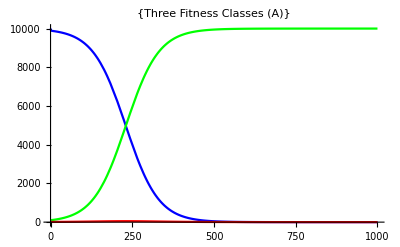

```mathematica
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for one fitness class but below popsize *)
genotypes={{1,1}};
genotypeabundances={10^4-500};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class (B)"}]
(* Testing system solver for one fitness class but above popsize *)
genotypes={{1,1}};
genotypeabundances={10^4+500};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class (A)"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-100-10,100,10};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
(* Testing system solver for three fitness class below popsize *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-500,100,10};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes (B)"}]
(* Testing system solver for three fitness class above popsize *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4,100,10};
{system,sol}=SolveDiffEqs[Δc1,Δc2,genotypeabundances,genotypes,nexttimestep,popsize]
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,nexttimestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes (A)"}]
```

```mathematica
(* Testing module that gets new mutants *)
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}
newmutantgenotypes=getNextMutants[genotypes]
newmutantgenotypes[[1]][[2]][[1]][[1]]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

6